## Maria José Domínguez Tarea #2

```mathematica
2.3.3
```

Ṅ=-aNln(bN)

Para el crecimiento de un tumor el parámetro a es una constante relacionada a la habilidad de las células cancerígenas de reproducirse y b es la capacidad de carga .
Haciendo Ṅ=0 para hallar los puntos fijos N* del sistema (en términos de los parámetros), se sigue que:

-aNln(bN)=0 ⇒ Nln(bN)=0

como N no puede ser igual a cero, pues ln(0) no está definida, se sigue que:

ln(bN)=0 ⇒ bN= ⅇ^0 ⇒ N=1/b

El sistema posee entonces solo un punto fijo en N*=1/b, por la grafica de N vs Ṅ, podemos ver que el flujo  a ambos lados de N* va hacia él, a su vez, lo cual implica que es un punto fijo inestable, en la gráfica de soluciones se puede verificar.

```mathematica
eq1= {T'[t]== -a*T[t]*Log[b*T[t]]};
var1= {T[t]};
cond1= {T[0]==1};
para1 = {a-> 2, b-> 4};
s1= NDSolve[Flatten[{eq1/.para1, cond1}], var1, {t,0,20}];
Manipulate[Show[Plot[-a*T*Log[b*T], {T,0,5}, Frame->True,PlotLegends->{"Ṅ=-aNln(bN)"},AxesLabel->{"x","ẋ"}]],{a,0,15},{b,0,5}]
```

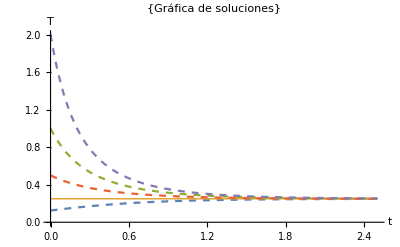

```mathematica
sol1= DSolve[Flatten[{eq1/.para1, T[0]==c}], var1, {t,0,20}];
Plot[Evaluate[T[t]/.sol1/.{{c->1/8},{c-> 1/4},{c-> 1},{c-> 1/2},{c-> 2}}], {t,0,2.5}, PlotRange->{0,2},PlotStyle->{Dashed,Thick,Dashed,Dashed,Dashed},AxesLabel->{"t","T"},PlotLabel->{"Gráfica de soluciones"}]
```

### 3.4.1

ẋ= rx+4x.b3

Nuevamente, haciendo ẋ=0 para hallar los puntos fijos x*:

ẋ=0 ⇒ rx+4x.b3=0 ⇒ x(r+4x.b2)=0

De aqui se sigue que x*=0 es un punto fijo para cualquier valor de r. Analizando ahora el término entre paréntesis:

r+4x.b2=0 ⇒  x.b2= -r/4 ⇒ x= ±√-r/2

Como la expresión anterior solo es real para r<0, se sigue que el sistema presenta dos puntos fijos x*= ±√r/2 para r<0.
Analizando la grafica de x vs ẋ vemos que la estabilidad de x*=0 depende de r, siendo estable para r<0 e inestable para r>0, a su vez, x*= ±√r/2 son puntos inestables, estos análisis se verifican con las gráficas de soluciones para r<0 y r>0, por el diagrama de bifurcación vemos que se trata de una bifurcación de tenedor subcrítica para r<0, resultado ya anticipado pues la ecuacion es de la forma ẋ=rx+x.b3, forma general para dicha bifurcación.

```mathematica
eq2={x'[t]==r*x[t]+4*(x[t])^3};
var2={x[t]};
cond2={x[0]==10};
para2={r->-4};
para3= {r-> 6};
```

```mathematica
Manipulate[Show[Plot[r*x+4*x^3,{x,-2,2},AxesLabel->{"x","ẋ"}],Graphics[{PointSize[0.03], Point[{x,r*x+4*x^3}/.Solve[r*x+4*x^3==0,x, Reals], VertexColors->{Red, Green}]}],VectorPlot[{Sign[r*x+4*x^3],0}, {x,-2,2},{y,-10,10},VectorStyle->{Gray,"Arrow"},VectorScale->0.02, RegionFunction->Function[{x,y,vx,vy,n}, -1<y<1] ]],{r,-10,10}]
```

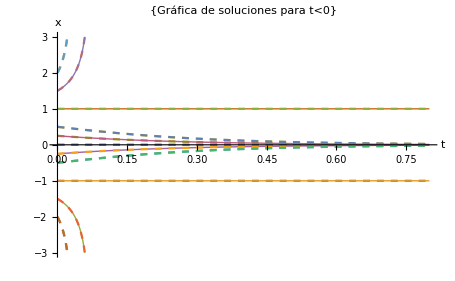

```mathematica
sol2=DSolve[Flatten[{eq2/.para2, x[0]==c1}], var2, {t,-3,3}]
Plot[Evaluate[var2/.sol2/.{{c1->-2},{c1-> -1.5},{c1-> -1},{c1-> -1/2},{c1-> -1/4},{c1-> 0},{c1-> 1/4},{c1-> 1/2},{c1-> 1},{c1-> 1.5},{c1-> 2}}], {t,0,0.8}, PlotRange->{-3,3}, PlotLabel->{"Gráfica de soluciones para t<0"},PlotStyle->{Dashed, Dashed,Thick,Dashed,Dashed,Thick, Dashed, Dashed, Thick, Dashed,Dashed},AxesLabel->{"t","x"}]
```

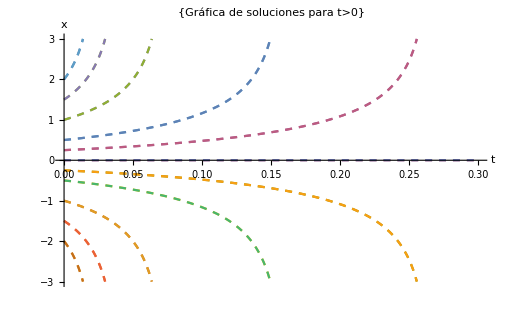

```mathematica
sol3= DSolve[Flatten[{eq2/.para3, x[0]==c1}], var2, {t,-3,3}]
Plot[Evaluate[var2/.sol3/.{{c1->-2},{c1-> -1.5},{c1-> -1},{c1-> -1/2},{c1-> -1/4},{c1-> 0},{c1-> 1/4},{c1-> 1/2},{c1-> 1},{c1-> 1.5},{c1-> 2}}], {t,0,0.3}, PlotRange->{-3,3}, PlotLabel->{"Gráfica de soluciones para t>0"},PlotStyle->{Dashed, Dashed,Dashed,Dashed,Dashed,Dashed, Dashed, Dashed,Dashed, Dashed,Dashed},AxesLabel->{"t","x"}]
```

```mathematica
Reduce[r*x+4*(x)^3==0,x]
```

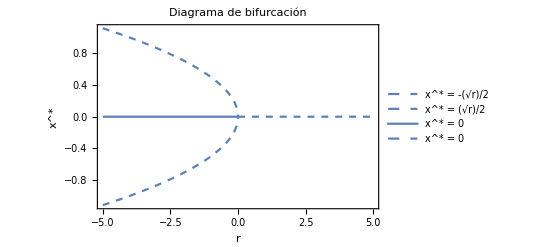

```mathematica
f1[r_]:= -(ⅈ √r)/2
f2[r_]:= (ⅈ √r)/2
f3[r_]:= 0
F1= Plot[f1[r], {r,-5,5},Frame->True, PlotRange->All, PlotStyle->Dashed,PlotLegends->{"x^* = -(√r)/2"}, AxesLabel->{Style["r",20],Style["x^*",20]}];
F2=Plot[f2[r],{r,-5,5},Frame->True, PlotRange->All, PlotStyle->Dashed,PlotLegends->{"x^* = (√r)/2"},AxesLabel->{Style["r",20],Style["x^*",20]}];
F3=Plot[f3[r],{r,-5,0},Frame->True, PlotRange->All, PlotStyle->Thick,PlotLegends->{"x^* = 0"},AxesLabel->{Style["r",20],Style["x^*",20]}];
F4=Plot[f3[r],{r,0,5},Frame->True, PlotRange->All, PlotStyle->Dashed,PlotLegends->{"x^* = 0"},AxesLabel->{Style["r",20],Style["x^*",20]}];
Show[F1,F2,F3,F4, PlotLabel-> "Diagrama de bifurcación"]
```

### 3.4.14

ẋ= rx+x.b3-x⁵

haciendo ẋ=0 para hallar los puntos fijos x*:

ẋ=0 ⇒ rx+x.b3-x⁵=0 ⇒ x(r+x.b2-x⁴)=0

De aquí se sigue que x*=0 es un punto fijo para cualquier r, haciendo u=x.b2  ⇒ u.b2=x⁴ para analizar el término en paréntesis:

r+u+u.b2=0 ⇒ u= (-1±√(1-4r))/2 ⇒ x.b2= (-1±√(1-4r))/2 ⇒ x*=±√((-1±√(1-4r))/2)

Esta ecuación es una representación canónica de un sistema con bifurcación a tenedor subcrítica. A diferencia de la ecuación 3.4.1, el término x⁵ es un término estabilizador, por el cual las ramas inestables pasan a ser estables para un valor dado de r= r_s, hecho apreciable en el diagrama de bifurcación; estas ramas estables existen para cualquier r> r_s. De la gráfica de x vs ẋ se puede ver que para r< r_s x*=0 es estable localmente y es el único punto fijo del sistema. Vemos además que r_s=-0.25 y que para r_s<r⩽-0.1 x*=0 es inestable y aparecen los otros 4 puntos fijos, los cuales colapsan a dos puntos fijos para r>-0.1 .

```mathematica
eq3= {x'[t]==r*x[t]+(x[t])^3-(x[t])^5};
var3= {x[t]};
cond3= {x[0]==1};
par3= {r->4};
par4= {r-> -4};
par5= {r-> -0.1};
Manipulate[Show[Plot[r*x+x^3-x^5,{x,-2.5,2.5},AxesLabel->{"x","ẋ"}], Graphics[{PointSize[0.03], Point[{x,r*x+x^3-x^5}/.Solve[r*x+x^3-x^5==0,x, Reals], VertexColors->{Red, Green}]}] ,VectorPlot[{Sign[r*x+4*x^3],0}, {x,-2.5,2.5},{y,-10,10},VectorStyle->{Gray,"Arrow"},VectorScale->0.02, RegionFunction->Function[{x,y,vx,vy,n}, -1<y<1] ]],{r,-10,10}]
```

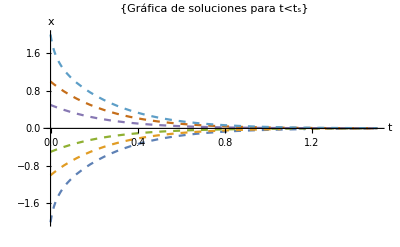

```mathematica
sn1= DSolve[Flatten[{eq3/.par4, x[0]==d}], var3, {t,-2,2}]
Plot[Evaluate[var3/.sn1/.{{d->-2},{d-> -1},{d-> -1/2},{d-> 0},{d-> 1/2},{d-> 1},{d-> 2}}], {t,0,1.5}, PlotRange->{-2,2}, PlotLabel->{"Gráfica de soluciones para t<t_s"},PlotStyle->{Dashed, Dashed,Dashed,Thick,Dashed,Dashed, Dashed},AxesLabel->{"t","x"}]
```

{{x[t]→InverseFunction[1/272 (-68 Log[#1]-(-17+√17) Log[1+√17-2 #1^2]+(17+√17) Log[-1+√17+2 #1^2])&][-t+1/272 (-68 Log[d1]-(-17+√17) Log[1+√17-2 d1^2]+(17+√17) Log[-1+√17+2 d1^2])]}}

ReplaceAll::reps: {(d→2) (d11→1.8)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {(d→2.) (d11→1.8)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

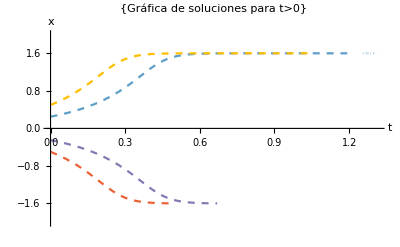

```mathematica
sn2= DSolve[Flatten[{eq3/.par3, x[0]==d1}], var3, {t,-2,2}]
Plot[Evaluate[var3/.sn2/.{{d1->-2},{d1->-1.8},{d1-> -√(1/2 (1+√17))},{d1-> -1/2},{d1-> -1/4},{d1->0},{d1-> 1/4},{d1-> 1/2},{d1-> √(1/2 (1+√17))},{d11->1.8}{d-> 2}}], {t,0,1.5}, PlotRange->{-2,2}, PlotLabel->{"Gráfica de soluciones para t>0"},PlotStyle->{Dashed, Dashed,Thick,Dashed,Dashed,Thick, Dashed,Dashed,Thick,Dashed,Dashed},AxesLabel->{"t","x"}]
```

x==0||x==-(√(1-√(1+4 r)))/(√2)||x==(√(1-√(1+4 r)))/(√2)||x==-(√(1+√(1+4 r)))/(√2)||x==(√(1+√(1+4 r)))/(√2)

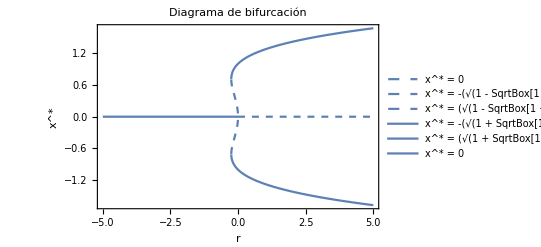

```mathematica
Reduce[r x+x^3-x^5==0,x]
f5[r_]:=0
f6[r_]:= -(√(1-√(1+4 r)))/(√2)
f7[r_]:=(√(1-√(1+4 r)))/(√2)
f8[r_]:=-(√(1+√(1+4 r)))/(√2)
f9[r_]:=(√(1+√(1+4 r)))/(√2)
F5=Plot[f5[r],{r,0,5},Frame->True, PlotRange->All, PlotStyle->Dashed,PlotLegends->{"x^* = 0"},AxesLabel->{Style["r",20],Style["x^*",20]}];
F6=Plot[f6[r],{r,-5,5},Frame->True, PlotRange->All, PlotStyle->Dashed,PlotLegends->{"x^* = -(√(1 - SqrtBox[1 + 4 r]))/(√2)"},AxesLabel->{Style["r",20],Style["x^*",20]}];
F7=Plot[f7[r],{r,-5,5},Frame->True, PlotRange->All, PlotStyle->Dashed,PlotLegends->{"x^* = (√(1 - SqrtBox[1 + 4 r]))/(√2)"},AxesLabel->{Style["r",20],Style["x^*",20]}];
F8=Plot[f8[r],{r,-5,5},Frame->True, PlotRange->All, PlotStyle->Thick,PlotLegends->{"x^* = -(√(1 + SqrtBox[1 + 4 r]))/(√2)"},AxesLabel->{Style["r",20],Style["x^*",20]}];
F9=Plot[f9[r],{r,-5,5},Frame->True, PlotRange->All, PlotStyle->Thick,PlotLegends->{"x^* = (√(1 + SqrtBox[1 + 4 r]))/(√2)"},AxesLabel->{Style["r",20],Style["x^*",20]}];
F10= Plot[f5[r],{r,-5,0},Frame->True, PlotRange->All, PlotStyle->Thick,PlotLegends->{"x^* = 0"},AxesLabel->{Style["r",20],Style["x^*",20]}];
Show[F5,F6,F7,F8,F9,F10, PlotLabel-> "Diagrama de bifurcación"]
```